```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Peak Theory scale-inv.

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0,n^2-1>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[n,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2]

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(2-2 Cos[kW r])/(kW^2 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamman[n_]=sigman[n,kW,As]^2/(sigman[n-1,kW,As]sigman[n+1,kW,As])//Simplify
Rn[n_,kW_]=√3 sigman[n,kW,As]/sigman[n+1,kW,As]//Simplify
```

(√(-1+n^2))/n

(√(3+3/n))/kW

```mathematica
1/x^2 D[(x^2 D[psin[1,x,kW], x]), x]+(sigman[2,kW,As]/sigman[1,kW,As])^2 psin[2,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[2,x,kW], x]), x]+(sigman[3,kW,As]/sigman[2,kW,As])^2 psin[3,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[3,x,kW], x]), x]+(sigman[4,kW,As]/sigman[3,kW,As])^2 psin[4,x,kW]//Simplify
```

0

```mathematica
zetax[x_,mu2_,kappa_]=mu2(1/(1-gamman[3]^2)(psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW])-kappa^2/(gamman[3](1-gamman[3]^2))(gamman[3]^2 psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW]))//Simplify
```

-(6 mu2 (-8+6 √2 kappa^2-3 x^2+2 √2 kappa^2 x^2+(8-x^2+√2 kappa^2 (-6+x^2)) Cos[x]-2 (-4+3 √2 kappa^2) x Sin[x]))/x^4

```mathematica
zetaLap[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetax[x,mu,kappa], x]), x]//Simplify
```

(6 mu (96-72 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+(-96+42 x^2-x^4+√2 kappa^2 (72-32 x^2+x^4)) Cos[x]-2 x (48-5 x^2+4 √2 kappa^2 (-9+x^2)) Sin[x]))/x^6

```mathematica
Normal[Series[-kW^2 zetaLap[x,mu,kappa](sigman[1,kW,As]/sigman[2,kW,As])^2,{x,0,1}]]
```

mu

```mathematica
zetaLL[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetaLap[x,mu,kappa], x]), x]//Simplify
```

-1/x^8 6 mu (-72 (40+x^2)+48 √2 kappa^2 (45+x^2)+(2880-1368 x^2+84 x^4-x^6+√2 kappa^2 (-2160+1032 x^2-66 x^4+x^6)) Cos[x]-2 x (-6 (240-34 x^2+x^4)+√2 kappa^2 (1080-156 x^2+5 x^4)) Sin[x])

```mathematica
Normal[Series[kW^4 zetaLL[x,mu,kappa]/mu(sigman[1,kW,As]/sigman[2,kW,As])^2 sigman[2,kW,As]/sigman[4,kW,As],{x,0,1}]]
```

kappa^2

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-1/x^8(-192 mu+144 √2 kappa^2 mu-36 mu x^2+24 √2 kappa^2 mu x^2+x^4+12 mu (16-5 x^2+4 √2 kappa^2 (-3+x^2)) Cos[x]+6 mu x (32-x^2+√2 kappa^2 (-24+x^2)) Sin[x])^2)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

64-48 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+1/2 (-128+52 x^2-x^4+√2 kappa^2 (96-40 x^2+x^4)) Cos[x]-1/2 x (128-11 x^2+3 √2 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->50]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.6592083883523112147945417748657759700612077960189

5.3701421552991077958189118888035944434174892377781

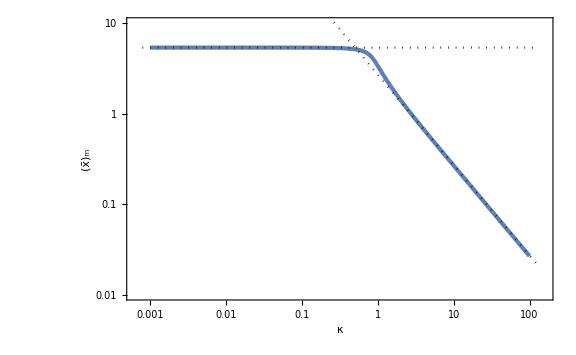

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.7/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==267/1000,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

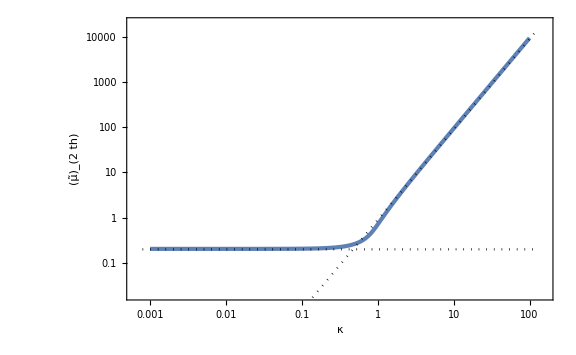

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.2,0.9 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

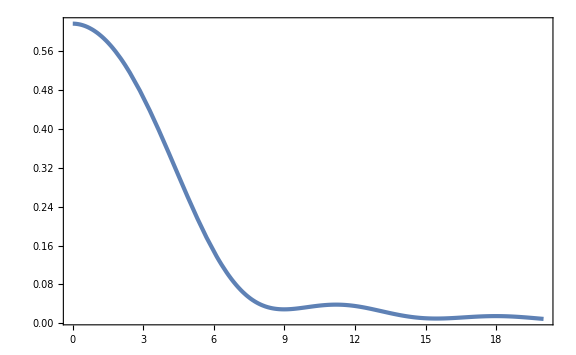

```mathematica
Plot[zetax[x,muthint[k],k]/.{k->0.1},{x,0.01,20},PlotRange->Full]
```

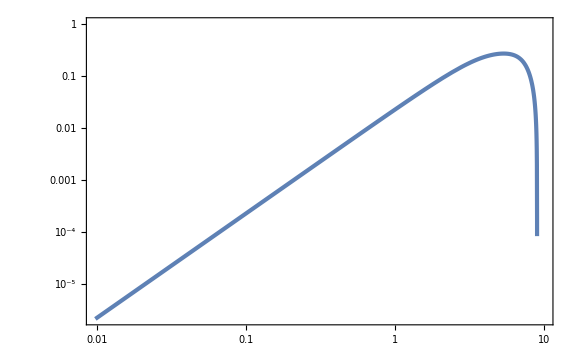

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10^-1},{x,0,10},WorkingPrecision->50]
```

```mathematica
muthint[10]
```

93.716374899296789123751056186879802506929152269

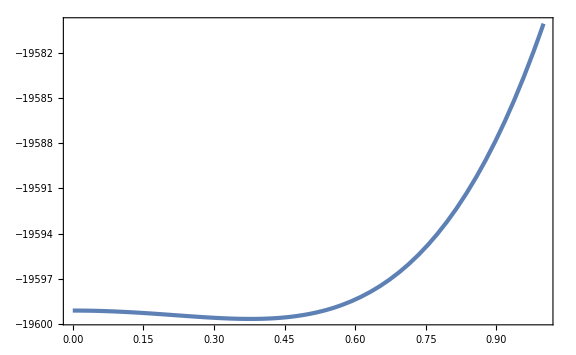

```mathematica
Plot[zetax[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50]
```

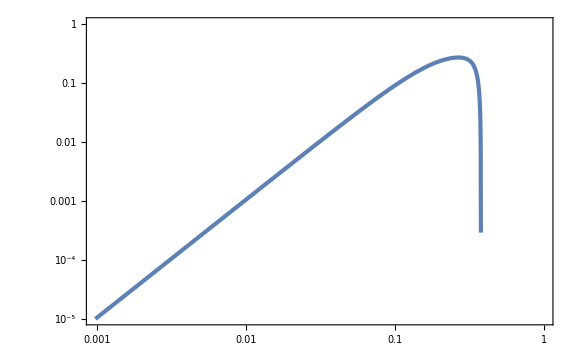

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50]
```

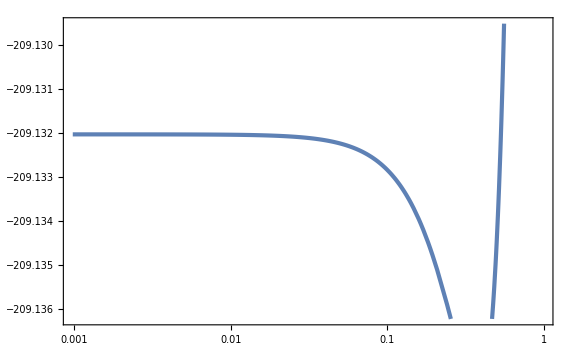

```mathematica
LogLinearPlot[zetax[x,1,k]/.{k->10},{x,0,1},WorkingPrecision->50]
```

```mathematica
Normal[Series[-zetaLap[x,1,100](sigman[1,1,As]/sigman[2,1,As])^2,{x,0,1}]]
```

1

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

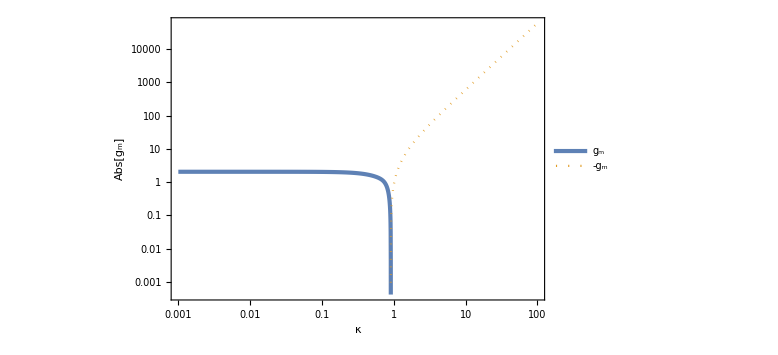

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

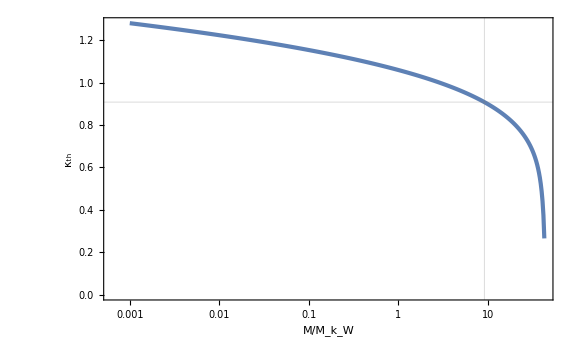

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
sigmamu=(kW^4/sigman[2,kW,As]^2)^(-1/2)//Simplify
```

(√As)/2

```mathematica
kappa2mean=sigman[3,kW,As]^2/sigman[2,kW,As]^2 1/kW^2//Simplify
```

2/3

```mathematica
sigmakappa=((mu^2 kW^4 kW^4)/(sigman[4,kW,As]^2(1-gamma3^2)))^(-1/2)//Simplify
```

(√As)/(6 √2 mu)

```mathematica
CC=1/kW^3 2/(6π)^(3/2)mu kW^2 kappa kW sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)(sigmamu sigmakappa)/(√(1-gamma3^2))kW^3//Simplify
```

kappa/(8 √2 π^(3/2))

```mathematica
zz=(mu kW^2 kappa^2 kW^2)/sigman[4,kW,As]//Simplify
```

(2 √2 kappa^2 mu)/(√As)

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

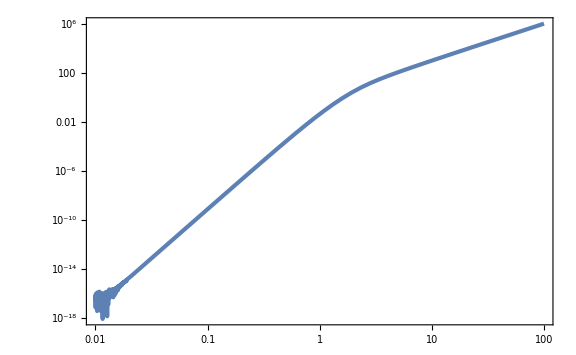

```mathematica
LogLogPlot[f[z],{z,10^-2,10^2}]
```

```mathematica
npk[mu_,kappa_,As_]=CC f[zz]PG[mu,0,sigmamu^2]PG[kappa^2,kappa2mean,sigmakappa^2]kappa//Simplify
```

1/(4 As π^(5/2))3 ⅇ^(-(6 (3-8 kappa^2+6 kappa^4) mu^2)/As) kappa^2 mu (ⅇ^(-(20 kappa^4 mu^2)/As) (-8/5+(4 kappa^4 mu^2)/As+ⅇ^((15 kappa^4 mu^2)/As) (8/5+(62 kappa^4 mu^2)/As)) √(2/(5 π))+(√2 kappa^2 mu (-3 As+8 kappa^4 mu^2) (Erf[(√5 kappa^2 mu)/(√As)]+Erf[(2 √5 kappa^2 mu)/(√As)]))/As^(3/2))

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,1 10^-2]},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3]},{logM,1,2,10^-2}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{95.3225,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{91.445,Null}

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

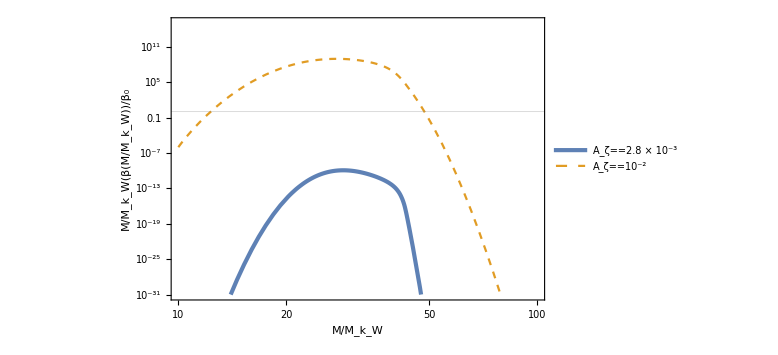

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.82,0.85}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[2]]
```

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(InterpolatingFunction[{{1.,2.}},{5,7,0,{101},{4},0,0,0,0,Automatic,«3»},{{1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,«91»}},«1»,{Automatic}][Log[MM]/Log[10]]) MM)) is less than WorkingPrecision (30.).

1.15519760805973494735148652629×10^-10

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(InterpolatingFunction[{{1.,2.}},{5,7,0,{101},{4},0,0,0,0,Automatic,«3»},{{1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,«91»}},«1»,{Automatic}][Log[MM]/Log[10]]) MM)) is less than WorkingPrecision (30.).

28.8015410141770510451550102994

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2976.45 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2531.34 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2135.1 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

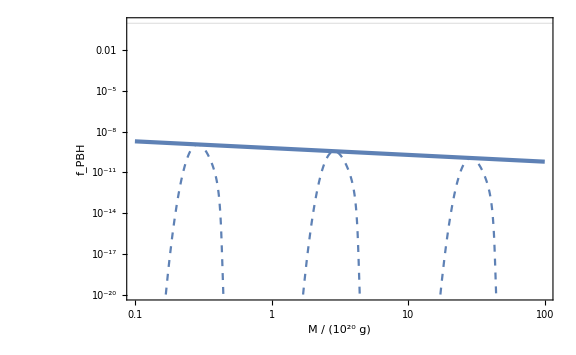

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
Integrand[z_]=WTH[k R]^2(k R)^4 TrsT[k R]^2/.{k->z/R}//Simplify
```

(243 (-z Cos[z]+Sin[z])^2 (√3 z Cos[z/(√3)]-3 Sin[z/(√3)])^2)/z^8

```mathematica
NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

5.36981

```mathematica
sigmad2[As_]=16/81 As NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

1.0607 As

```mathematica
betaPBH[As_]=1/2 Erfc[dth/(√(2sigmad2[As]))]/.{dth->0.267 2};
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,As_]=betaPBH[As]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,As]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3}
```

{1.32039×10^19,2.18112×10^-7}

```mathematica
fPBHPSList=Table[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
```

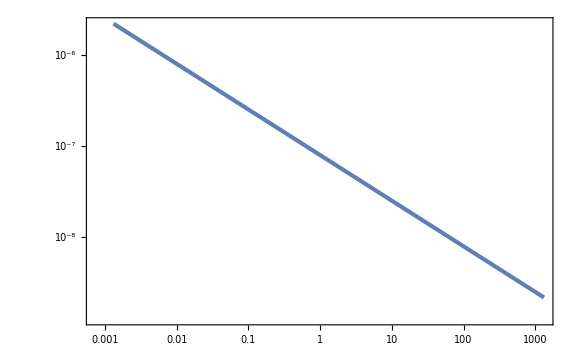

```mathematica
ListLogLogPlot[fPBHPSList]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2976.45 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2531.34 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2135.1 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

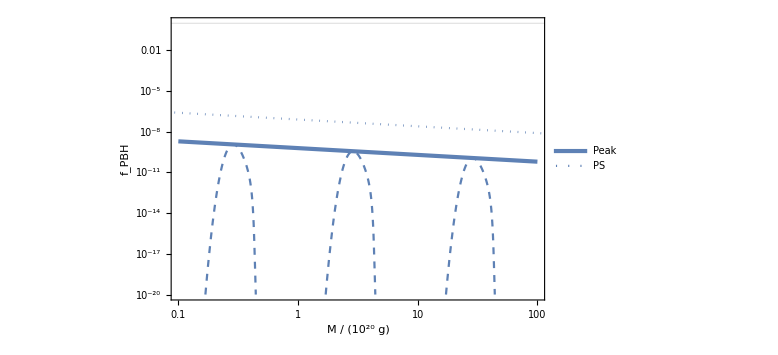

```mathematica
Show[LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2),0},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[{None,None,None,"Peak","PS"},{0.8,0.8}],FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}],ListLogLogPlot[fPBHPSList,PlotStyle->{Dotted}]]
```

## monochromatic

```mathematica
npeak=2^4;
NL=256;
```

### test

```mathematica
mapdata=Import["data/mono_map_0.dat"][[1]];
```

```mathematica
Variance[mapdata]
```

1.01368

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

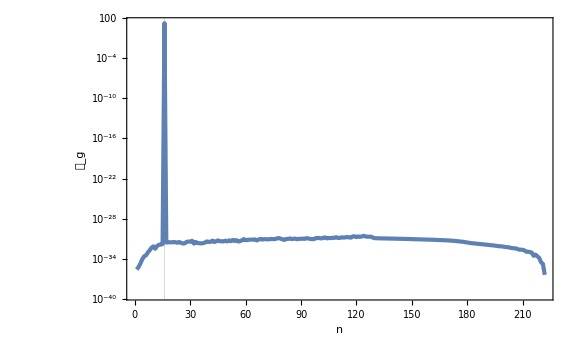

```mathematica
ListLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]}]
```

```mathematica
powerList[[17]]
```

{16,16.2188}

```mathematica
biasedmap=Import["data/mono_biased_0.dat"][[1]];
lapmap=Import["data/mono_laplacian_0.dat"][[1]];
```

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

### importance sampling

```mathematica
mukdata=Import["data/mono_muk.dat"];
Ntot=Length[mukdata]
```

10000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data,ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[μ], 2],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data,ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[k], 3],"log_10𝒲"}]
```

-Graphics-

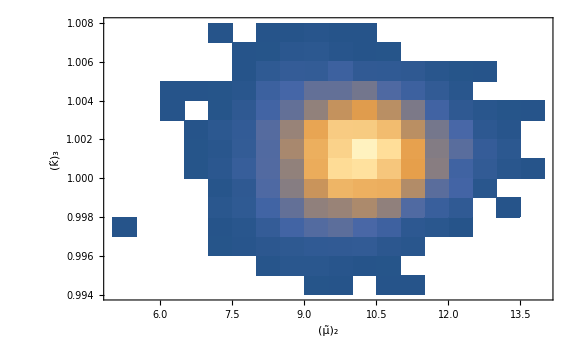

```mathematica
DensityHistogram[mukdata[[All,2;;3]],FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverTilde[k], 3]}]
```

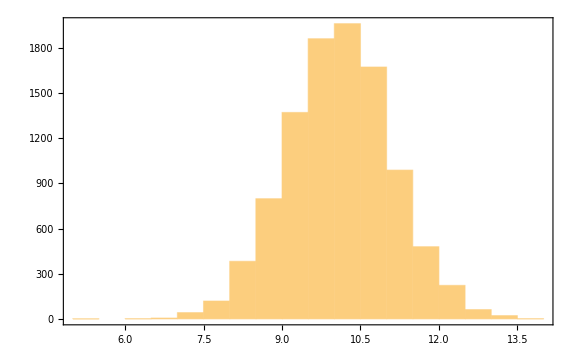

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/2

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

5

14

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
```

```mathematica
PSmu2List=Table[{mu2,Length[mu2binning[mu2]]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

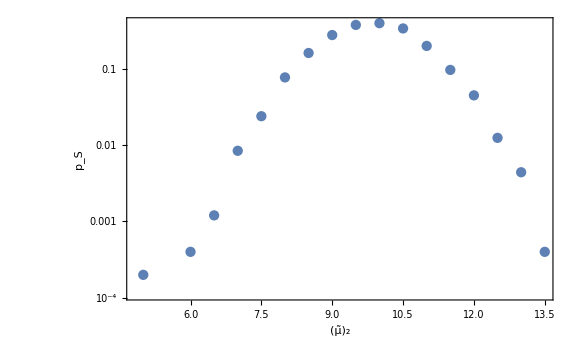

```mathematica
ListLogPlot[PSmu2List,Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

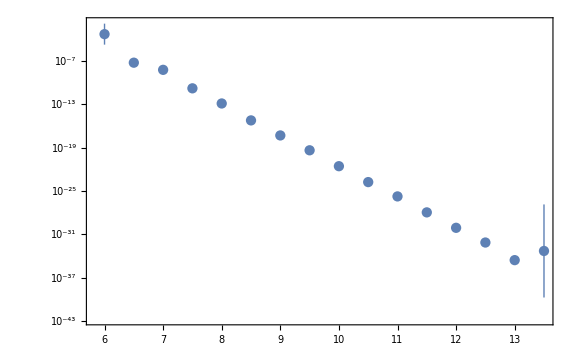

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
PTmu2List=Table[{PSmu2List[[i,1]],PSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[PSmu2List]}];
```

```mathematica
σ1=2π npeak;
σ2=(2π npeak)^2;
σ3=(2π npeak)^3;
σ4=(2π npeak)^4;
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
Pmu2PT[mu2_]=1/(6π)^(3/2)(σ2^2 σ4^3)/(σ1^4 σ3^3) f[σ2/σ1^2 mu2] 1/Sqrt[2π] Exp[-mu2^2/2];
```

```mathematica
f[10]//N
```

970.

```mathematica
((2π)/3)^(3/2)f[10]//N
```

2940.08

```mathematica
(NL/npeak)^3
```

4096

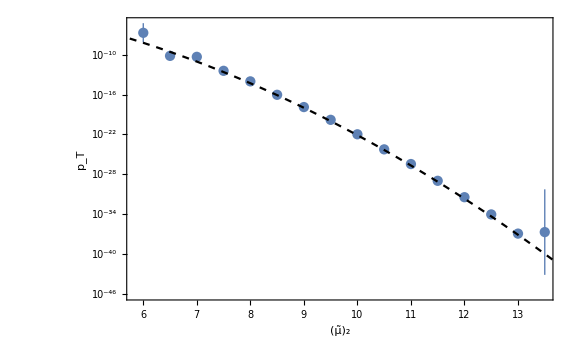

```mathematica
Show[ListLogPlot[PTmu2List,Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[1/Sqrt[2π] Exp[-x^2/2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

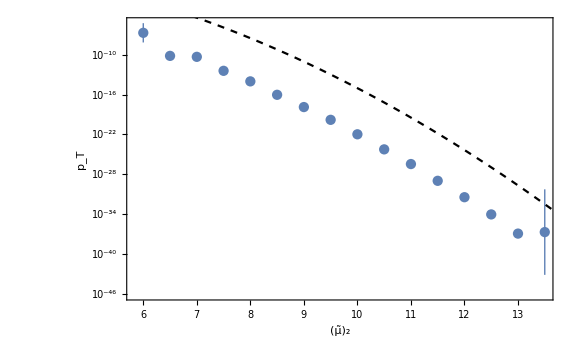

```mathematica
Show[ListLogPlot[PTmu2List,Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[Pmu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

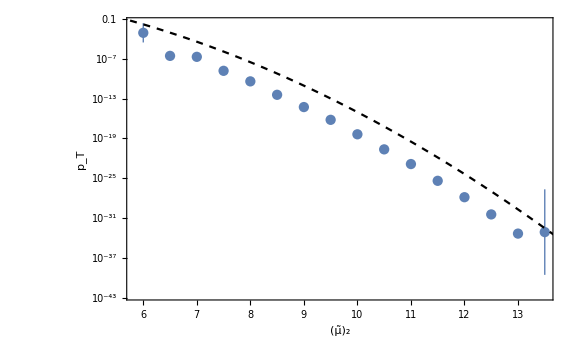

```mathematica
Show[ListLogPlot[PTmu2List.DiagonalMatrix[{1,npeak^3}],Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[Pmu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

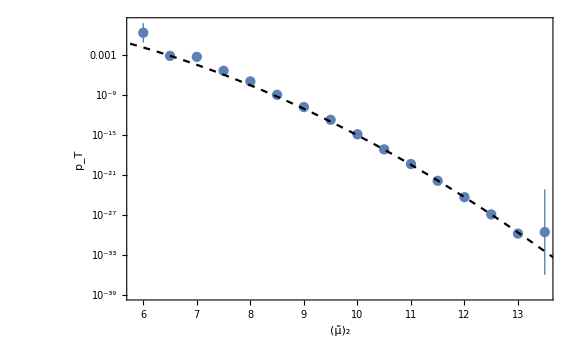

```mathematica
Show[ListLogPlot[PTmu2List.DiagonalMatrix[{1,3000 npeak^3}],Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[Pmu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

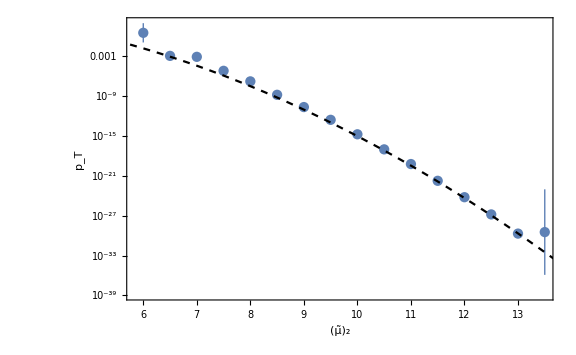

```mathematica
Show[ListLogPlot[PTmu2List.DiagonalMatrix[{1,NL^3}],Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[Pmu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
PTmu2List[[11]]
1/Sqrt[2π] Exp[-10^2/2]//N
```

{10,1.050.070.0810^-22}

7.6946×10^-23

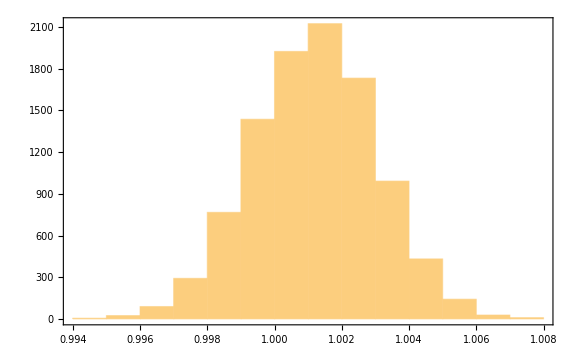

```mathematica
Histogram[mukdata[[All,3]]]
```